## Preamble

```mathematica
BeginPackage["cosmomathicaInterface`"]
```

```mathematica
transfer::usage="This function provides an interface to Eisensteins&Hu's fitting formula for the transfer function. It takes the reduced total matter density ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant as input, and returns the sound horizon, the peak k, the transfer function...";

halofit::usage="This function provides an interface to the halofit algorithm by Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: ...) at 20 different values of the scale factor and the convergence power spectrum in tabulated form.";

cosmicemu::usage="This function provides an interface to the CosmicEmulator by Earl Lawrence. It takes ω_M, ω_b, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as ...";

camb::usage="This function provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes Ω_C, ..., as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. The default options are ...";
```

```mathematica
Interface::CosmicEmu="Parameter out of bounds. `3` <= `1` <= `4` required, but `1`=`2`.";
```

```mathematica
CAMB::Tcmb="Temperature of the CMB (default:)";
```

```mathematica
CAMB::Eigenstates="NuMassEigenstates and NuMassFractions must have the same length  (can be zero).";
CAMB::InvalidOption="Option `1` is '`2`', but must be one of the following: `3`";
CAMB::Lists="The following options need to be non-empty lists of the same length: `1`";
CAMB::Error="CAMB exited with the following error code: `1`";
CAMB::LinkBroken="CAMB crashed. See if there is anything useful on stdout.";
```

## Main

```mathematica
Begin["`Private`"]
```

```mathematica
$location=DirectoryName[$InputFileName];
```

```mathematica
camb[OmegaC_?NumericQ,OmegaB_?NumericQ,OmegaL_?NumericQ,h_?NumericQ,w_?NumericQ,opts:OptionsPattern[]]:=Module[{link,result,resultfloat,resultint,floats,ints,bool2int,initialcond,nonlinear,massivenu,validateoption,validatelists,limits,check,getDimensions,dimensions,age,zre,array},

bool2int[b_]:=If[OptionValue@b,1,0];
validateoption[op_,poss_]:=If[!MemberQ[poss,OptionValue[op]],Message[CAMB::InvalidOption,ToString@op,OptionValue@op,StringJoin@@poss(*TODO fix the string*)];Return[$Failed];Abort[]];

getDimensions[list_]:=Module[{i,r},
i=1;r={};
While[i<Length@list,AppendTo[r,list[[i+1;;i+list[[i]]]]];i=i+1+list[[i]]];
r];


(*some parameters must be within certain limits*)
limits={{ReionizationFraction,0,1.5},{OpticalDepth,0,.9}};
check={#[[1]],#[[2]]≤OptionValue[#[[1]]]<=#[[3]]}&/@limits;

validatelists[ops_]:=If[1!=Length@Union[Length/@OptionValue/@ops],Message[CAMB::Lists,ops];Return[$Failed];Abort[]];
validatelists[{ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude}];
validatelists[{NuMassDegeneracies,NuMassFractions}];
(*If[Not[0≤OptionValue[ReionizationFraction]≤1.5],Abort[]]; (*TODO*)*)

initialcond={"vector","adiabatic","iso_CDM","iso_baryon","iso_neutrino","iso_neutrino_vel"};
nonlinear={"none","pk","cl"};
massivenu={"int","trunc","approx","best"};

validateoption[ScalarInitialCondition,initialcond];
validateoption[NonLinear,nonlinear];
validateoption[MassiveNuMethod,massivenu];

floats=Flatten@{OmegaC,OmegaB,OmegaL,h*100,OptionValue[#]&/@{OmegaNu,Tcmb,YHe,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude,PivotScalar,PivotTensor,OpticalDepth,ReionizationRedshift,ReionizationFraction,ReionizationDeltaRedshift,MaxEtaK,MaxEtaKTensor,TransferKmax,TransferRedshifts}};

ints=Flatten@{OptionValue[MassiveNeutrinos],Length@OptionValue[NuMassFractions],Position[initialcond,OptionValue[ScalarInitialCondition]][[1,1]]-1,Position[nonlinear,OptionValue[NonLinear]][[1,1]]-1,Length@OptionValue@ScalarSpectralIndex,bool2int/@{DoReionization,UseOpticalDepth,TransferHighPrecision,WantCMB,WantTransfer,WantCls,WantScalars,WantVectors,WantTensors,WantZstar, WantZdrag},OptionValue[#]&/@{OutputNormalization,MaxEll,MaxEllTensor,TransferKperLogInt},Length@OptionValue@TransferRedshifts,bool2int/@{AccuratePolarization,AccurateReionization,AccurateBB,DoLensing,OnlyTransfers,DerivedParameters},Position[massivenu,OptionValue[MassiveNuMethod]][[1,1]]-1};


SetDirectory[$location<>"ext/camb"];
link=Install[$location<>"ext/math_link"];
result=Global`CAMBrun[N/@floats,ints];
ResetDirectory[];
If[result==$Failed,Message[CAMB::LinkBroken];Return[$Failed];Abort[]];
Uninstall[link];

{resultfloat,resultint}=result;
If[resultint[[1]]≠0,Message[CAMB::Error,resultint[[1]]];Return[$Failed];Abort[]];
resultint=Drop[resultint,1];
dimensions=getDimensions@resultint;

{age,zre}=resultfloat[[;;2]];
resultfloat=Drop[resultfloat,2];

Do[array=Take[resultfloat,Times@@d];
resultfloat=Drop[resultfloat,Times@@d];
AppendTo[resultfloat,ArrayReshape[array,d]],{d,dimensions}];

{camb["Age"]->age,camb["zRec"]->zre,resultint,resultfloat}
];
Options[camb]={Tcmb->2.7255,OmegaNu->0,YHe->.24,MasslessNeutrinos->3.046,MassiveNeutrinos->0,NuMassDegeneracies->{0},NuMassFractions->{1},ScalarInitialCondition->"adiabatic",NonLinear->"none",WantCMB->True,WantTransfer->True,WantCls->True,ScalarSpectralIndex->{.96},ScalarRunning->{0},TensorSpectralIndex->{0},RatioScalarTensorAmplitudes->{1},ScalarPowerAmplitude->{2.1*^-9},PivotScalar->.05,PivotTensor->.05,DoReionization->True,UseOpticalDepth->False,OpticalDepth->0.,ReionizationRedshift->10.,ReionizationFraction->1.,ReionizationDeltaRedshift->.5,TransferHighPrecision->False,WantScalars->True,WantVectors->True,WantTensors->True,WantZstar->True, WantZdrag->True,OutputNormalization->1,MaxEll->1500,MaxEtaK->3000.,MaxEtaKTensor->800.,MaxEllTensor->400,TransferKmax->.9,TransferKperLogInt->0,TransferRedshifts->{0.},AccuratePolarization->True,AccurateReionization->False,AccurateBB->False,DoLensing->True,OnlyTransfers->False,DerivedParameters->True,MassiveNuMethod->"best"};
```

```mathematica
(*Transfer function*)
transfer[omegaM_?NumericQ,fBaryon_?NumericQ,Tcmb_?NumericQ,h_?NumericQ]:=Module[{result,link,krange,fitonek,horizon,peak},

link=Install[$location<>"ext/math_link"];

Global`TFSetParameters[N@omegaM,N@fBaryon,N@Tcmb];

fitonek[k_]:={Sequence@@Global`TFFitOneK[k],
Global`TFNoWiggles[N@omegaM,N@fBaryon,N@h,N@Tcmb,k],
Global`TFZeroBaryon[N@omegaM,N@h,N@Tcmb,k]}; 

krange=10^Range[-6.,4.,.01];
result=Transpose[fitonek/@krange];
horizon=Global`TFSoundHorizon[N@omegaM,N@fBaryon,N@h];
peak=Global`TFkPeak[N@omegaM,N@fBaryon,N@h];

Uninstall[link];

{transfer["soundhorizon"]->horizon,
transfer["peak"]->peak,
transfer["kvalues"]->krange,
 transfer["full"]->result[[1]],
transfer["baryon"]->result[[2]],
transfer["cdm"]->result[[3]],
transfer["nowiggles"]->result[[4]],
transfer["zerobaryons"]->result[[5]]}
];
```

```mathematica
halofit[OmegaM_?NumericQ,OmegaL_?NumericQ,gammaShape_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,betaP_?NumericQ,z0_?NumericQ]:=Module[{link,Tf={},Kappa={},arange,krange,ellrange},
link=Install[$location<>"ext/math_link"];

arange=Range[.01,.9999,.04]~Join~{.99999};
krange=10^Range[-4,3,.1];
ellrange=10^Range[-2,6,.1];

Do[
Global`HFSetParameters[N@OmegaM,N@OmegaL,N@gammaShape,N@sigma8,N@ns,N@betaP,N@z0,i];
AppendTo[Tf,Table[Global`HFGetPkNL[a,k],{a,arange},{k,krange}]];
AppendTo[Kappa,Table[Global`HFGetKappa[ell],{ell,ellrange}]],
{i,0,2}]

Uninstall[link];

(*Just return the raw numbers*)
{halofit["avalues"]->arange,
halofit["kvalues"]->krange,
halofit["ellvalues"]->ellrange,
halofit["kappaBBKS"]->Kappa[[1]],halofit["tfBBKS"]->Tf[[1]],
halofit["kappaPD96"]->Kappa[[2]],halofit["tfPD96"]->Tf[[2]],
halofit["kappaHalofit"]->Kappa[[3]],halofit["tfHalofit"]->Tf[[3]]}
];
```

```mathematica
cosmicemu[omegaM_?NumericQ,omegaB_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,w_?NumericQ]:=Module[{link,result,labels,limits,parameters,check},

labels={"ω_M","ω_b","n_s","σ_8","w"};
limits={{.12,.155},{.0214,.0235},{.85,1.05},{.61,.9},{-1.3,-.7}};
(*these are hard limits as given by the authors of the cosmic emulator - the program will crash if any parameter is outside its bounds*)
parameters={omegaM,omegaB,sigma8,ns,w};

check=(#[[2,1]]<=#[[1]]<=#[[2,2]])&/@Transpose[{parameters,limits}];
Do[If[!check[[i]],Message[Interface::CosmicEmu,labels[[i]],parameters[[i]],limits[[i,1]],limits[[i,2]]]],{i,Length@check}];
If[!And@@check,Return[$Failed];Abort[]];

link=Install[$location<>"ext/math_link"];
result=Table[{1/a-1,Global`CEGetPkNL[N@omegaM,N@omegaB,N@sigma8,N@ns,N@w,1/a-1]},{a,.5,1.,.1}];
 (*CosmicEmu only does these five redshifts, everything else is interpolated*)

Uninstall[link];

(*Just return the raw numbers*)
result
];
```

```mathematica
End[ ]
EndPackage[ ]
```

## Test

```mathematica
<<(NotebookDirectory[]<>"interface.m")
```

```mathematica
hfdata=halofit[.25,.75,.5,.8,.9,.7,1.5];
```

```mathematica
cedata=cosmicemu[.15,.022,.9,.9,-1];
```

```mathematica
tfdata=transfer[.15,.05,2.7,.7];
```

```mathematica
cambdata=camb[.2,.05,.75,.7,-1.,WantCls->True,WantScalars->True];
```

```mathematica
cambdata[[3]]
```

{3,1499,1,6,3,1499,1,4,3,399,1,4,1,67,2,67,1,2,67,1,2,1,1}

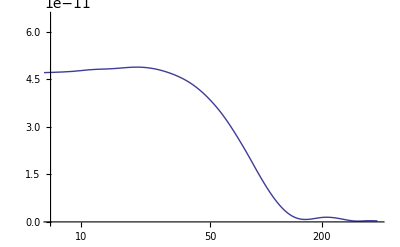

```mathematica
ListLogLinearPlot[cambdata[[4,3,All,1,1]],Joined->True]
```

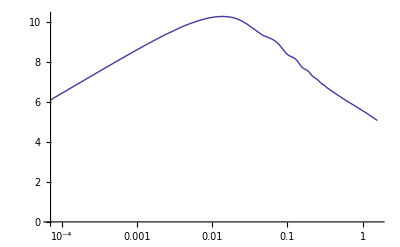

```mathematica
ListLogLinearPlot[Transpose@{Exp@cambdata[[4,4]],Flatten@cambdata[[4,6]]},Joined->True]
```

```mathematica
cambdata[[4,1]]
```

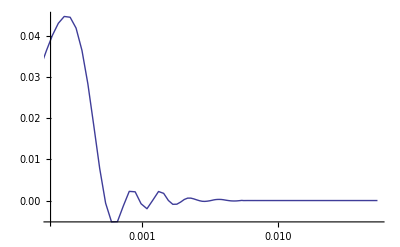

```mathematica
ListLogLinearPlot[Transpose@{cambdata[[4,5]],cambdata[[4,6,1,1]]},Joined->True,PlotRange->All]
```